```mathematica
(*Setup variables*)
n = RandomInteger[{3,6}];
poly = RandomPolygon[{"Convex",n}];
boundary = RegionBoundary[poly];
sides = Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ boundary));
centroid = RegionCentroid[poly];
ray = HalfLine[centroid,5*AngleVector[RandomReal[{0,2*Pi}]]];
breakPoint = RandomPoint @ boundary;
```

```mathematica
sideList[poly_] := Line /@ Partition[#,2,1]& @ Partition[#,2]& @ (Flatten @ (List @@ RegionBoundary[poly]));
```

```mathematica
getCurrentSide[poly_,point_] := Extract[#,{1}]& @ First @ SortBy[RegionDistance[#,point]&] @ sideList[poly];
```

```mathematica
lineToVecRep[line_] := (
line[[2]]-line[[1]]
);
```

```mathematica
(*Calculates raycast from an arbitrary starting point and angle in a polygon*)
castRayPolygon[poly_, point_,originVector_] := Module[{currentSide,ray,sides,collisions,pointOfCollision,oppRay,newDirection,possibleCollisions},
sides = sideList[poly];
currentSide = getCurrentSide[poly,point];
newDirection = calculateNewDirection[originVector,lineToVecRep[currentSide]];
ray = HalfLine[point,newDirection];
possibleCollisions =   (List @@ RegionIntersection[ray,RegionBoundary@ poly])[[1]];
pointOfCollision = Last @ (SortBy[EuclideanDistance[#,point]&][possibleCollisions]);
Echo[pointOfCollision];
collisionSide = Extract[#,{1}]& @ Last @ SortBy[sides, RegionDistance[#,pointOfCollision]&];
Return @ {pointOfCollision, currentSide,point,newDirection};
];
```

This function calculates the new direction vector of the ball based on the incoming direction and the side that it hit.

```mathematica
calculateNewDirection[originVector_, sideVec_]:= (
100*(2*Projection[originVector,sideVec]-originVector)
);
```

```mathematica
castInfo = castRayPolygon[poly, breakPoint, breakPoint-centroid];
newRay = Line[{castInfo[[3]],castInfo[[1]]}];
newCast = castRayPolygon[poly, castInfo[[1]],castInfo[[4]]];
Echo @ newCast
```

{-0.0487767,-0.0607207}

{0.0446317,0.0196068}

{2.17849,-7.47769}

{0.0139891,0.0702248}

{{0.0139891,0.0702248},{{0.,0.},{0.120596,0.052978}},{0.0446317,0.0196068},{-403.345,666.28}}

{{0.0139891,0.0702248},{{0.,0.},{0.120596,0.052978}},{0.0446317,0.0196068},{-403.345,666.28}}

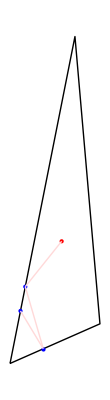

```mathematica
Graphics[{boundary, Red, Point[centroid],Blue,Point[castInfo[[3]]],LightRed,Line[{breakPoint,centroid}],Blue,LightRed,newRay,Blue,Point[castInfo[[1]]],Point[newCast[[1]]],LightRed,Line[{newCast[[3]],newCast[[1]]}]}]
```